```mathematica
numberOfTrials = 0; 
probability = 1;
scorePerThrow = 1; 
results = List[];
iterator = 0; 

While [iterator < 10000, 
target =RandomInteger[{385,405}];
baseScore = 390;
origBaseScore = 390; 
ratio = target/origBaseScore; 
While [  target>= baseScore-2.5 ∧ target <=baseScore+2.5,
		If [ RandomInteger[1] == 0,
			baseScore = baseScore + scorePerThrow,
			baseScore  = baseScore - scorePerThrow];
		probability = probability * 0.5; 
	];
(*If [baseScore == 385, Print["ONE HIT"]]; *)
AppendTo[results, {ratio,probability}];
probability = 1; 
iterator++; 
]
results;
```

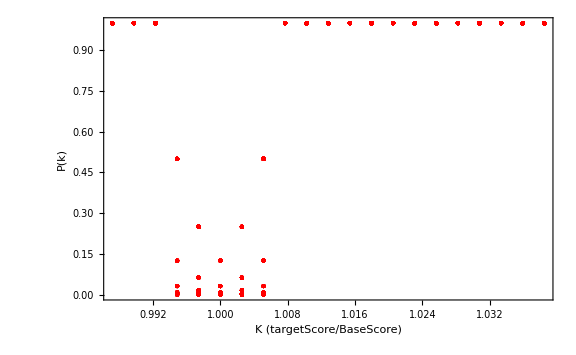

```mathematica
ListPlot[results,PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"K (targetScore/BaseScore) ","P(k)","",""}, LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
```